# Technology development

## In this scenario, technology is in development to turn zombies back to human.

This interactive model simulates how technological advancement 𝑇 alters the human–zombie dynamics by reversing interaction outcomes, and visualizes the resulting trajectories, phase flows, and local stability structure.

```mathematica
Manipulate[
 Module[
  {
   eqns, sol, H, Z, R, t, Hfunc, Zfunc, Rfunc,
   phasePlotHZ, phasePlotZR, jMatrix,
   detJ, finalDetJ, traceJ, finalTraceJ,
   rFix, hFix
  },

  (* Dimensionless system *)
  eqns = {
    H'[t] == (T - 1)*(1 - R[t])*H[t]*Z[t],
    Z'[t] == (1 - T)*(1 - R[t])*H[t]*Z[t],
    R'[t] == (c*(1 - R[t]) - gamma)*H[t]
  };

  (* Jacobian *)
  jMatrix = {
    { (T - 1)*(1 - R)*Z,   (T - 1)*(1 - R)*H,   -(T - 1)*H*Z },
    { (1 - T)*(1 - R)*Z,   (1 - T)*(1 - R)*H,   -(1 - T)*H*Z },
    { c*(1 - R) - gamma,   0,                  -c*H }
  };

  sol = NDSolve[
    {
     eqns,
     H[0] == H0,
     Z[0] == Z0,
     R[0] == R0
    },
    {H, Z, R},
    {t, 0, tmax},
    Method -> {"StiffnessSwitching"},
    MaxSteps -> Infinity
  ];

  Hfunc = H /. sol[[1]];
  Zfunc = Z /. sol[[1]];
  Rfunc = R /. sol[[1]];

  rFix = Rfunc[tmax];
  hFix = Hfunc[tmax];

  traceJ = Tr[jMatrix];
  detJ = Det[jMatrix];

  finalTraceJ = traceJ /. {
      H -> hFix, Z -> (Z[tmax] /. sol[[1]]), R -> rFix,
      T -> T, c -> c, gamma -> gamma
    };

  finalDetJ = detJ /. {
      H -> hFix, Z -> (Z[tmax] /. sol[[1]]), R -> rFix,
      T -> T, c -> c, gamma -> gamma
    };

  phasePlotHZ =
   StreamPlot[
    Evaluate[{
      (T - 1)*(1 - rFix)*H*Z,
      (1 - T)*(1 - rFix)*H*Z
    }],
    {H, 0, hMaxPlot}, {Z, 0, zMaxPlot},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    Frame -> True,
    FrameLabel -> {"H", "Z"}
   ];

  phasePlotZR =
   StreamPlot[
    Evaluate[{
      (1 - R)*Z*hFix*(1 - T),
      (c*(1 - R) - gamma)*hFix
    }],
    {Z, 0, zMaxPlot}, {R, 0, rMaxPlot},
    StreamStyle -> Directive[Arrowheads[0.02], Gray],
    StreamScale -> Medium,
    Frame -> True,
    FrameLabel -> {"Z", "R"}
   ];

  Column[{
    Plot[
     {Hfunc[t], Zfunc[t], Rfunc[t]},
     {t, 0, tmax},
     PlotRange -> All,
     PlotLegends -> {"H", "Z", "R"},
     PlotStyle -> {{Blue, Thick}, {Red, Thick}, {Purple, Thick}},
     Frame -> True,
     FrameLabel -> {"t", "H, Z, R"}
    ],
    phasePlotHZ,
    phasePlotZR,
    ListPlot[
     {{finalDetJ, finalTraceJ}},
     PlotRange -> {{-10, 10}, {-10, 10}},
     PlotStyle -> {Red, PointSize[Large]},
     Frame -> True,
     FrameLabel -> {"Determinant", "Trace"}
    ]
   }]
 ],

 (* ========================= *)
 (* FIXED PARAMETER RANGES   *)
 (* ========================= *)

 (* T must hit 1 easily *)
 {{T, 1, "T̂"}, 0, 2, 0.01},

 (* c positive *)
 {{c, 1.0, "ĉ"}, 0.1, 5, 0.01},

 (* gamma must satisfy gamma <= c to keep R>=0 *)
 {{gamma, 0.5, "γ̂"}, 0, Dynamic[c], 0.01},

 Delimiter,

 {{H0, 1, "H0"}, 0, 10, 0.1},
 {{Z0, 0.2, "Z0"}, 0, 10, 0.1},

 (* R always 0 to 1 *)
 {{R0, 0.5, "R0"}, 0, 1, 0.01},

 Delimiter,

 {{tmax, 50, "tmax"}, 1, 500, 1},

 Delimiter,

 {{hMaxPlot, 2, "H plot max"}, 0.1, 10, 0.1},
 {{zMaxPlot, 2, "Z plot max"}, 0.1, 10, 0.1},
 {{rMaxPlot, 1, "R plot max"}, 0.1, 2, 0.01}
]
```

## Eigenvalues Calculation

Defines the Jacobian and computes eigenvalues at each fixed-point family to determine stability.

```mathematica
jMatrix = {
  { (T - 1)*(1 - R)*Z,   (T - 1)*(1 - R)*H,   -(T - 1)*H*Z },
  { (1 - T)*(1 - R)*Z,   (1 - T)*(1 - R)*H,   -(1 - T)*H*Z },
  { c*(1 - R) - gamma,   0,                  -c*H }
};

(* Fixed point families *)
fixedPoint1 = {H -> 0};                            (* Extinction *)
fixedPoint2 = {Z -> 0, R -> 1 - gamma/c};          (* Total victory *)
fixedPoint3 = {T -> 1, R -> 1 - gamma/c};          (* Coexistence *)

(* Eigenvalues for each fixed point *)
eigenVals1 = Eigenvalues[jMatrix /. fixedPoint1]
eigenVals2 = Eigenvalues[jMatrix /. fixedPoint2]
eigenVals3 = Eigenvalues[jMatrix /. fixedPoint3]
```

{0,0,-((-1+R) (-1+T) Z)}

{0,-c H,-(gamma H (-1+T))/c}

{-c H,0,0}

{-H,0,0}

## Bifurcation Analysis

This code performs a bifurcation sweep over the technology parameter 𝑇, numerically integrating the system for each value and plotting the resulting long-term human and zombie populations.

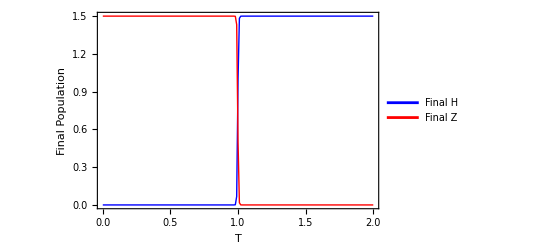

```mathematica
finalValuesT = Table[
  With[{Tv = Tval},   (* safe numerical substitution *)
   Module[
    {sol, Hfunc, Zfunc, finalH, finalZ, eqns},

    eqns = {
      H'[t] == (Tv - 1)*(1 - R[t])*H[t]*Z[t],
      Z'[t] == (1 - Tv)*(1 - R[t])*H[t]*Z[t],
      R'[t] == (c*(1 - R[t]) - gamma)*H[t]
    } /. {c -> 1.0, gamma -> 0.5};   (* ensure numeric c, gamma *)

    sol = NDSolve[
      {
       eqns,
       H[0] == 1.0,
       Z[0] == 0.5,
       R[0] == 0.5
      },
      {H, Z, R},
      {t, 0, 500},
      Method -> {"StiffnessSwitching"},
      MaxSteps -> Infinity
    ];

    Hfunc = H /. sol[[1]];
    Zfunc = Z /. sol[[1]];

    finalH = Hfunc[500];
    finalZ = Zfunc[500];

    {Tv, finalH, finalZ}
   ]
  ],
  {Tval, 0, 2, 0.01}
];

Tvalues      = finalValuesT[[All, 1]];
finalHValues = finalValuesT[[All, 2]];
finalZValues = finalValuesT[[All, 3]];

ListLinePlot[
 {
  Transpose[{Tvalues, finalHValues}],
  Transpose[{Tvalues, finalZValues}]
 },
 PlotRange -> All,
 PlotLegends -> {"Final H", "Final Z"},
 PlotStyle -> {{Blue, Thick}, {Red, Thick}},
 Frame -> True,
 FrameLabel -> {"T", "Final Population"}
]
```

## Stability Analysis - Variables

This code performs a sensitivity analysis by sweeping the initial conditions  and examining how the system’s long-term human, zombie, and resource levels change.

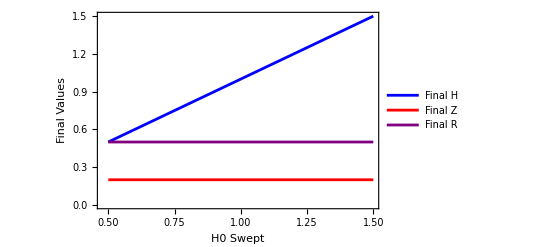
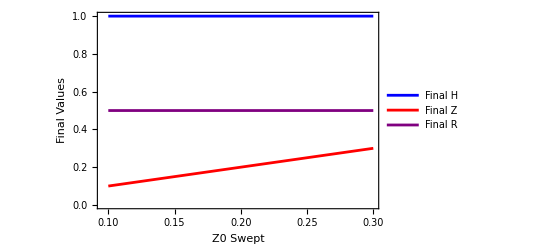
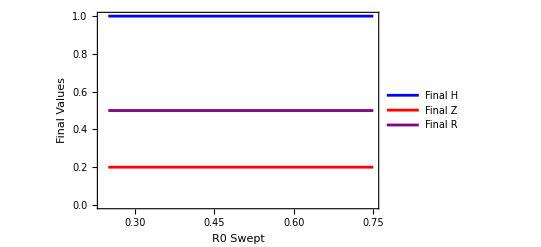

```mathematica
(* ============================== *)
(* Sensitivity sweep parameters   *)
(* ============================== *)

T = 1;
c = 1;
gamma = 0.5;

H0 = 1;
Z0 = 0.2;
R0 = 0.5;
tmax = 50;

icRange = 0.5;  (* ±50% sweep *)

(* ------------------------------- *)
(* 1. Sweep H0                     *)
(* ------------------------------- *)

H0sweep = Table[
  Module[{sol, Hfunc, Zfunc, Rfunc},

   eqns = {
     H'[t] == (T - 1)*(1 - R[t])*H[t]*Z[t],
     Z'[t] == (1 - T)*(1 - R[t])*H[t]*Z[t],
     R'[t] == (c*(1 - R[t]) - gamma)*H[t]
   };

   sol = NDSolve[
     {
      eqns,
      H[0] == H0var,
      Z[0] == Z0,
      R[0] == R0
     },
     {H, Z, R},
     {t, 0, tmax}
   ];

   Hfunc = H /. sol[[1]];
   Zfunc = Z /. sol[[1]];
   Rfunc = R /. sol[[1]];

   {H0var, Hfunc[tmax], Zfunc[tmax], Rfunc[tmax]}
  ],

  {H0var, H0*(1 - icRange), H0*(1 + icRange), (H0*2*icRange)/20}
];

H0plot = ListLinePlot[
  {
   Transpose[{H0sweep[[All, 1]], H0sweep[[All, 2]]}],
   Transpose[{H0sweep[[All, 1]], H0sweep[[All, 3]]}],
   Transpose[{H0sweep[[All, 1]], H0sweep[[All, 4]]}]
  },
  PlotLegends -> {"Final H", "Final Z", "Final R"},
  Frame -> True,
  FrameLabel -> {"H0 Swept", "Final Values"},
  PlotStyle -> {Blue, Red, Purple}
];

(* ------------------------------- *)
(* 2. Sweep Z0                     *)
(* ------------------------------- *)

Z0sweep = Table[
  Module[{sol, Hfunc, Zfunc, Rfunc},

   eqns = {
     H'[t] == (T - 1)*(1 - R[t])*H[t]*Z[t],
     Z'[t] == (1 - T)*(1 - R[t])*H[t]*Z[t],
     R'[t] == (c*(1 - R[t]) - gamma)*H[t]
   };

   sol = NDSolve[
     {
      eqns,
      H[0] == H0,
      Z[0] == Z0var,
      R[0] == R0
     },
     {H, Z, R},
     {t, 0, tmax}
   ];

   Hfunc = H /. sol[[1]];
   Zfunc = Z /. sol[[1]];
   Rfunc = R /. sol[[1]];

   {Z0var, Hfunc[tmax], Zfunc[tmax], Rfunc[tmax]}
  ],

  {Z0var, Z0*(1 - icRange), Z0*(1 + icRange), (Z0*2*icRange)/20}
];

Z0plot = ListLinePlot[
  {
   Transpose[{Z0sweep[[All, 1]], Z0sweep[[All, 2]]}],
   Transpose[{Z0sweep[[All, 1]], Z0sweep[[All, 3]]}],
   Transpose[{Z0sweep[[All, 1]], Z0sweep[[All, 4]]}]
  },
  PlotLegends -> {"Final H", "Final Z", "Final R"},
  Frame -> True,
  FrameLabel -> {"Z0 Swept", "Final Values"},
  PlotStyle -> {Blue, Red, Purple}
];

(* ------------------------------- *)
(* 3. Sweep R0                     *)
(* ------------------------------- *)

R0sweep = Table[
  Module[{sol, Hfunc, Zfunc, Rfunc},

   eqns = {
     H'[t] == (T - 1)*(1 - R[t])*H[t]*Z[t],
     Z'[t] == (1 - T)*(1 - R[t])*H[t]*Z[t],
     R'[t] == (c*(1 - R[t]) - gamma)*H[t]
   };

   sol = NDSolve[
     {
      eqns,
      H[0] == H0,
      Z[0] == Z0,
      R[0] == R0var
     },
     {H, Z, R},
     {t, 0, tmax}
   ];

   Hfunc = H /. sol[[1]];
   Zfunc = Z /. sol[[1]];
   Rfunc = R /. sol[[1]];

   {R0var, Hfunc[tmax], Zfunc[tmax], Rfunc[tmax]}
  ],

  {R0var, R0*(1 - icRange), R0*(1 + icRange), (R0*2*icRange)/20}
];

R0plot = ListLinePlot[
  {
   Transpose[{R0sweep[[All, 1]], R0sweep[[All, 2]]}],
   Transpose[{R0sweep[[All, 1]], R0sweep[[All, 3]]}],
   Transpose[{R0sweep[[All, 1]], R0sweep[[All, 4]]}]
  },
  PlotLegends -> {"Final H", "Final Z", "Final R"},
  Frame -> True,
  FrameLabel -> {"R0 Swept", "Final Values"},
  PlotStyle -> {Blue, Red, Purple}
];

(* ------------------------------- *)
(* Display the three plots         *)
(* ------------------------------- *)

Column[{H0plot, Z0plot, R0plot}]
```

## Stability analysis - parameters

This script performs parameter sweeps of 𝑇, 𝑐, and 𝛾 around their nominal values, numerically simulates the H–Z–R system for each parameter value, and plots the resulting final human, zombie, and resource levels.

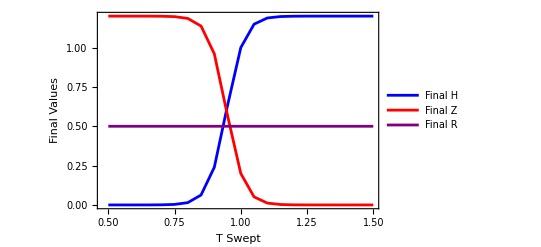
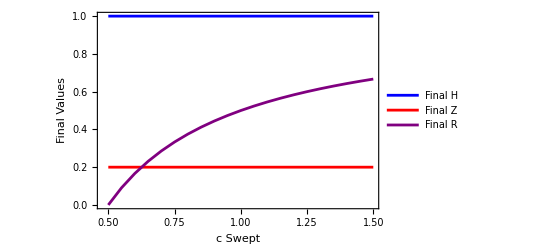
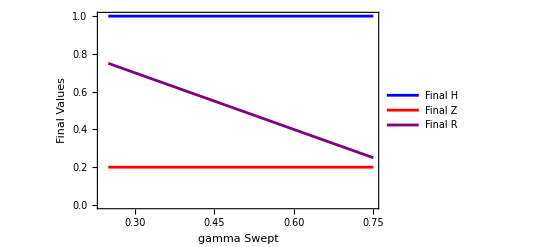

```mathematica
ClearAll["Global`*"]

(* Base parameters *)
Tpar = 1;
cpar = 1;
gampar = 0.5;

(* Initial values *)
H0 = 1;
Z0 = 0.2;
R0 = 0.5;

tmax = 50;
prange = 0.5; (* ±50% sweep *)


runSim[param_] := Module[
  {
    Tp = param["Tpar"],
    cp = param["cpar"],
    gp = param["gampar"],
    sol, Hf, Zf, Rf
  },

  eqns = {
    H'[t] == (Tp - 1)*(1 - R[t])*H[t]*Z[t],
    Z'[t] == (1 - Tp)*(1 - R[t])*H[t]*Z[t],
    R'[t] == (cp*(1 - R[t]) - gp)*H[t]
  };

  sol = NDSolve[
    {
      eqns,
      H[0] == H0,
      Z[0] == Z0,
      R[0] == R0
    },
    {H, Z, R},
    {t, 0, tmax}
  ][[1]];

  Hf = H[tmax] /. sol;
  Zf = Z[tmax] /. sol;
  Rf = R[tmax] /. sol;

  {Tp, cp, gp, Hf, Zf, Rf}
];

(* ---------------------------------------------- *)
(* 1. Sweep Tpar                                   *)
(* ---------------------------------------------- *)

TparSweep = Table[
  runSim[<|"Tpar" -> Tv, "cpar" -> cpar, "gampar" -> gampar|>],
  {Tv, Tpar*(1 - prange), Tpar*(1 + prange), (Tpar*2*prange)/20}
];

Tplot = ListLinePlot[
  {
    Transpose[{TparSweep[[All, 1]], TparSweep[[All, 4]]}],
    Transpose[{TparSweep[[All, 1]], TparSweep[[All, 5]]}],
    Transpose[{TparSweep[[All, 1]], TparSweep[[All, 6]]}]
  },
  PlotLegends -> {"Final H", "Final Z", "Final R"},
  Frame -> True,
  FrameLabel -> {"T Swept", "Final Values"},
  PlotStyle -> {Blue, Red, Purple}
];

(* ---------------------------------------------- *)
(* 2. Sweep cpar                                   *)
(* ---------------------------------------------- *)

cparSweep = Table[
  runSim[<|"Tpar" -> Tpar, "cpar" -> cv, "gampar" -> gampar|>],
  {cv, cpar*(1 - prange), cpar*(1 + prange), (cpar*2*prange)/20}
];

cplot = ListLinePlot[
  {
    Transpose[{cparSweep[[All, 2]], cparSweep[[All, 4]]}],
    Transpose[{cparSweep[[All, 2]], cparSweep[[All, 5]]}],
    Transpose[{cparSweep[[All, 2]], cparSweep[[All, 6]]}]
  },
  PlotLegends -> {"Final H", "Final Z", "Final R"},
  Frame -> True,
  FrameLabel -> {"c Swept", "Final Values"},
  PlotStyle -> {Blue, Red, Purple}
];

(* ---------------------------------------------- *)
(* 3. Sweep gampar                                 *)
(* ---------------------------------------------- *)

gamSweep = Table[
  runSim[<|"Tpar" -> Tpar, "cpar" -> cpar, "gampar" -> gv|>],
  {gv, gampar*(1 - prange), gampar*(1 + prange), (gampar*2*prange)/20}
];

gamplot = ListLinePlot[
  {
    Transpose[{gamSweep[[All, 3]], gamSweep[[All, 4]]}],
    Transpose[{gamSweep[[All, 3]], gamSweep[[All, 5]]}],
    Transpose[{gamSweep[[All, 3]], gamSweep[[All, 6]]}]
  },
  PlotLegends -> {"Final H", "Final Z", "Final R"},
  Frame -> True,
  FrameLabel -> {"gamma Swept", "Final Values"},
  PlotStyle -> {Blue, Red, Purple}
];

(* ---------------------------------------------- *)
(* Show all three plots                            *)
(* ---------------------------------------------- *)

Column[{Tplot, cplot, gamplot}]
```